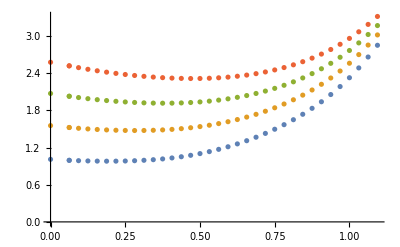

```mathematica
a={{0,1.009623},{0.062500,0.993650},{0.062500,0.993650},{0.093750,0.988067},{0.125000,0.983904},{0.156250,0.981180},{0.187500,0.979994},{0.218750,0.980498},{0.250000,0.982885},{0.281250,0.987382},{0.312500,0.994245},{0.343750,1.003756},{0.375000,1.016221},{0.406250,1.031961},{0.437500,1.051310},{0.468750,1.074600},{0.500000,1.102143},{0.531250,1.134202},{0.562500,1.170962},{0.593750,1.212514},{0.625000,1.258891},{0.656250,1.310160},{0.687500,1.366479},{0.718750,1.428107},{0.750000,1.495403},{0.781250,1.568841},{0.812500,1.649032},{0.843750,1.736748},{0.875000,1.832932},{0.906250,1.938701},{0.937500,2.055304},{0.968750,2.184100},{1.000000,2.326664},{1.031250,2.485068},{1.062500,2.661063},{1.093750,2.850275}};
a2={{0,1.553963},{0.062500,1.523385},{0.062500,1.523385},{0.093750,1.510792},{0.125000,1.500183},{0.156250,1.491407},{0.187500,1.484412},{0.218750,1.479221},{0.250000,1.475916},{0.281250,1.474620},{0.312500,1.475491},{0.343750,1.478716},{0.375000,1.484505},{0.406250,1.493084},{0.437500,1.504693},{0.468750,1.519578},{0.500000,1.537988},{0.531250,1.560169},{0.562500,1.586362},{0.593750,1.616801},{0.625000,1.651722},{0.656250,1.691361},{0.687500,1.735976},{0.718750,1.785852},{0.750000,1.841327},{0.781250,1.902806},{0.812500,1.970788},{0.843750,2.045892},{0.875000,2.128878},{0.906250,2.220666},{0.937500,2.322342},{0.968750,2.435144},{1.000000,2.560459},{1.031250,2.699794},{1.062500,2.853842},{1.093750,3.017274}};
a3={{0,2.072422},{0.062500,2.027617},{0.062500,2.027617},{0.093750,2.007008},{0.125000,1.988687},{0.156250,1.972511},{0.187500,1.958348},{0.218750,1.946135},{0.250000,1.935867},{0.281250,1.927589},{0.312500,1.921384},{0.343750,1.917371},{0.375000,1.915696},{0.406250,1.916529},{0.437500,1.920060},{0.468750,1.926495},{0.500000,1.936054},{0.531250,1.948968},{0.562500,1.965478},{0.593750,1.985835},{0.625000,2.010298},{0.656250,2.039141},{0.687500,2.072655},{0.718750,2.111157},{0.750000,2.155000},{0.781250,2.204589},{0.812500,2.260399},{0.843750,2.322992},{0.875000,2.393046},{0.906250,2.471373},{0.937500,2.558930},{0.968750,2.656820},{1.000000,2.766278},{1.031250,2.888579},{1.062500,3.024233},{1.093750,3.168459}};
a4={{0,2.576375},{0.062500,2.518407},{0.062500,2.518407},{0.093750,2.489565},{0.125000,2.462990},{0.156250,2.438744},{0.187500,2.416691},{0.218750,2.396725},{0.250000,2.378787},{0.281250,2.362866},{0.312500,2.348993},{0.343750,2.337236},{0.375000,2.327693},{0.406250,2.320490},{0.437500,2.315779},{0.468750,2.313731},{0.500000,2.314539},{0.531250,2.318412},{0.562500,2.325577},{0.593750,2.336276},{0.625000,2.350768},{0.656250,2.369329},{0.687500,2.392259},{0.718750,2.419882},{0.750000,2.452557},{0.781250,2.490689},{0.812500,2.534742},{0.843750,2.585253},{0.875000,2.642858},{0.906250,2.708306},{0.937500,2.782474},{0.968750,2.866371},{1.000000,2.961121},{1.031250,3.067879},{1.062500,3.187216},{1.093750,3.315377}};
ListPlot[{a,a2,a3,a4}]
```

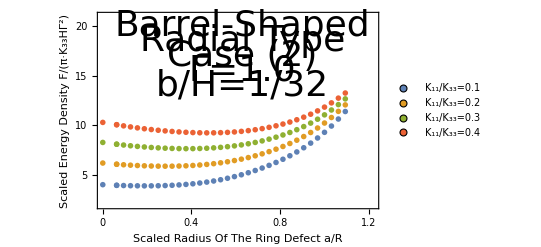

```mathematica
aa=a*Table[{1,4},{i,0,35}];
aa2=a2*Table[{1,4},{i,0,35}];
aa3=a3*Table[{1,4},{i,0,35}];
aa4=a4*Table[{1,4},{i,0,35}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{5,10,15,20},None},{{0,0.2, 0.4, 0.6, 0.8,1,1.2},None}}, PlotRange->{{0,1.22},{2,21}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.63,20}],Text[Style["Radial Type",Directive[Black,36]],{0.63,18.5}],Text[Style["Case (2)",Directive[Black,36]],{0.63,17}],Text[Style["Γ=1.0",Directive[Black,36]],{0.63,15.5}],Text[Style["b/H=1/32",Directive[Black,36]],{0.63,14}]}]
```